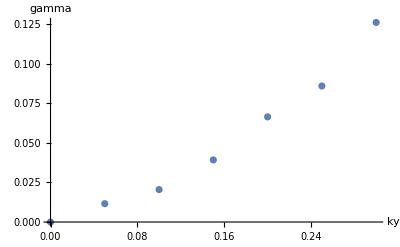

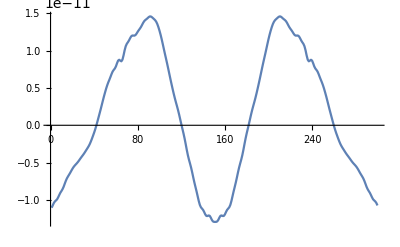

```mathematica
file="/Users/rogeriojorge/Downloads/w7x_linear.nc";
Import[file,"Datasets"];
phi=Import[file,{"Datasets","phi"}][[All,1,All,All]];
omega=Import[file,{"Datasets","omega_v_time"}][[All,1,All,All]];
ky=Import[file,{"Datasets","ky"}];
gammaVsKy=Table[Last@omega[[All,kyn,2]],{kyn,1,Length[ky]}];
ListPlot[Transpose@{ky,gammaVsKy},AxesLabel->{"ky","gamma"}]
ListLinePlot[{phi[[All,7,2]]},PlotRange->All]
```

```mathematica
Dimensions@omega
```

{25,34,2}

{0.,0.0228978,-0.0609627,0.0281521,0.0621662,0.0797242,0.10825,0.138294,0.151334,0.166205,0.182653,0.222064,0.265791,0.307377,0.346519,0.382768,0.415692,0.445033,0.470483,0.492054,0.509652,0.523367,0.533453,0.54014,0.,0.,0.,0.539538,0.534185,0.527679,0.520554,0.513233,0.505929,0.498859}